# Progetto di Matematica computazionale

```mathematica
(*Trasforma una stringa nella lista di codici ascii corrispondenti*)
inputString="lmiao";
asciiList =ToCharacterCode[inputString]
```

{108,109,105,97,111}

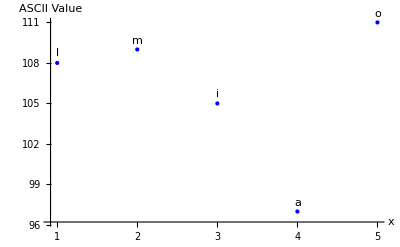

```mathematica
points = Transpose[{Range[Length[asciiList]],asciiList}];
charList=Characters[inputString];
labeledPoints=Transpose[{points,charList}];
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
```

126-(167 x)/4+(791 x^2)/24-(41 x^3)/4+(25 x^4)/24

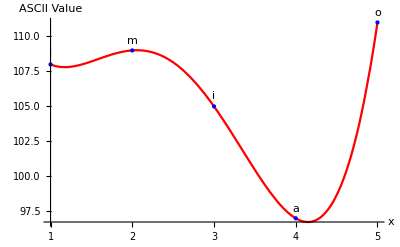

```mathematica
polynomial = Expand[InterpolatingPolynomial[points, x]]
Show[Plot[polynomial,{x,1,Length[asciiList]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium], Blue}]]
```

lmiaoÆƲΘ۶ౣᒏ⁃ち䗤懠

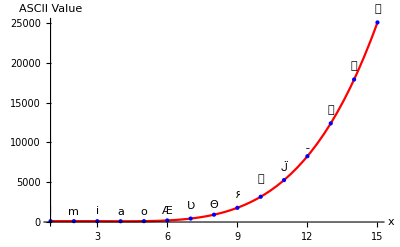

```mathematica
maxErrors = 10;
expandedPoints=Table[{i,polynomial/. x->i},{i,Length[points]+maxErrors}];
asciiListExpanded=Round[Last/@expandedPoints];
stringExpanded = FromCharacterCode[asciiListExpanded]
charListExpanded=FromCharacterCode/@asciiListExpanded;
labeledPointsExpanded=Transpose[{expandedPoints,charListExpanded}];
labeledPointsExpandedList=Labeled[#[[1]],#[[2]],Above]&/@labeledPointsExpanded;
Show[Plot[polynomial,{x,1,Length[expandedPoints]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsExpandedList,PlotStyle->{PointSize[Medium],Blue}]]
```

```mathematica
nErrors = RandomInteger[{1,maxErrors}]
errorsPos= RandomSample[Range[StringLength[stringExpanded]],nErrors]

myStringAsList=Characters[stringExpanded];
myStringAsList=Delete[myStringAsList,List/@errorsPos];
corruptedString=StringJoin[myStringAsList]
```

5

{12,14,2,3,1}

aoÆƲΘ۶ౣᒏち懠

```mathematica
strLen = StringLength[stringExpanded]
```

15

## ...

```mathematica
(*msg_received =  [corruptedString, errorsPos, strLen, maxErrors];*)
```

{97,111,198,434,920,1782,3171,5263,12385,25056}

{4,5,6,7,8,9,10,11,13,15}

{{4,97},{5,111},{6,198},{7,434},{8,920},{9,1782},{10,3171},{11,5263},{13,12385},{15,25056}}

{{{4,97},a},{{5,111},o},{{6,198},Æ},{{7,434},Ʋ},{{8,920},Θ},{{9,1782},۶},{{10,3171},ౣ},{{11,5263},ᒏ},{{13,12385},ち},{{15,25056},懠}}

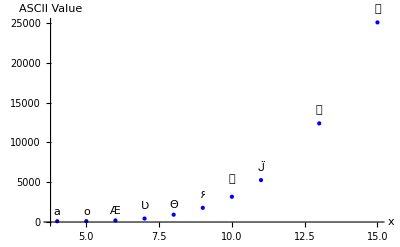

126-(167 x)/4+(791 x^2)/24-(41 x^3)/4+(25 x^4)/24

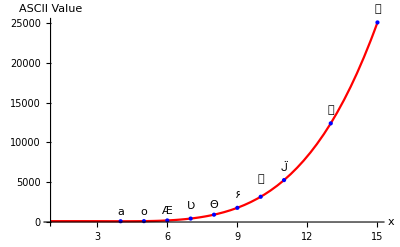

```mathematica
asciiList =ToCharacterCode[corruptedString]
charList = Characters[corruptedString];
charsPos=Complement[Range[strLen], errorsPos]
points = Transpose[{charsPos,asciiList}]
labeledPoints=Transpose[{points,charList}]
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
reconstructedPoly = Expand[InterpolatingPolynomial[points,x]]
Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]]
```

```mathematica
reconstructedPoints = Table[{i,polynomial/. x->i},{i,strLen-maxErrors}];
reconstructedAsciiList=Round[Last/@reconstructedPoints]
```

{108,109,105,97,111}

```mathematica
reconstructedString = FromCharacterCode[reconstructedAsciiList]
```

lmiao